```mathematica
<<SPQR`
```

SPℚR: loaded successfully

## Envelope

```mathematica
u = x[1]*x[2]*x[3] + x[1]*x[2]*x[4] + x[1]*x[2]*x[6] + x[1]*x[3]*x[4] + x[1]*x[3]*x[5] + x[1]*x[3]*x[6] + x[1]*x[4]*x[5] + x[1]*x[5]*x[6] + x[2]*x[3]*x[4] + x[2]*x[3]*x[5] + x[2]*x[4]*x[5] + x[2]*x[4]*x[6] + x[2]*x[5]*x[6] + x[3]*x[4]*x[6] + x[3]*x[5]*x[6] + x[4]*x[5]*x[6] // ReplaceAll[x[i_]:>ToExpression[StringJoin["x",ToString[i]]]]
f = -m2*x[1]^2*x[2]*x[3] - m2*x[1]^2*x[2]*x[4] - m2*x[1]^2*x[2]*x[6] - m2*x[1]^2*x[3]*x[4] - m2*x[1]^2*x[3]*x[5] - m2*x[1]^2*x[3]*x[6] - m2*x[1]^2*x[4]*x[5] - m2*x[1]^2*x[5]*x[6] - m2*x[1]*x[2]^2*x[3] - m2*x[1]*x[2]^2*x[4] - m2*x[1]*x[2]^2*x[6] - m2*x[1]*x[2]*x[3]^2 + (-4*m2 - s - t)*x[1]*x[2]*x[3]*x[4] - 3*m2*x[1]*x[2]*x[3]*x[5] - 3*m2*x[1]*x[2]*x[3]*x[6] - m2*x[1]*x[2]*x[4]^2 - 3*m2*x[1]*x[2]*x[4]*x[5] - 3*m2*x[1]*x[2]*x[4]*x[6] - 3*m2*x[1]*x[2]*x[5]*x[6] - m2*x[1]*x[2]*x[6]^2 - m2*x[1]*x[3]^2*x[4] - m2*x[1]*x[3]^2*x[5] - m2*x[1]*x[3]^2*x[6] - m2*x[1]*x[3]*x[4]^2 - 3*m2*x[1]*x[3]*x[4]*x[5] - 3*m2*x[1]*x[3]*x[4]*x[6] - m2*x[1]*x[3]*x[5]^2 + (-4*m2 + s)*x[1]*x[3]*x[5]*x[6] - m2*x[1]*x[3]*x[6]^2 - m2*x[1]*x[4]^2*x[5] - m2*x[1]*x[4]*x[5]^2 - 3*m2*x[1]*x[4]*x[5]*x[6] - m2*x[1]*x[5]^2*x[6] - m2*x[1]*x[5]*x[6]^2 - m2*x[2]^2*x[3]*x[4] - m2*x[2]^2*x[3]*x[5] - m2*x[2]^2*x[4]*x[5] - m2*x[2]^2*x[4]*x[6] - m2*x[2]^2*x[5]*x[6] - m2*x[2]*x[3]^2*x[4] - m2*x[2]*x[3]^2*x[5] - m2*x[2]*x[3]*x[4]^2 - 3*m2*x[2]*x[3]*x[4]*x[5] - 3*m2*x[2]*x[3]*x[4]*x[6] - m2*x[2]*x[3]*x[5]^2 - 3*m2*x[2]*x[3]*x[5]*x[6] - m2*x[2]*x[4]^2*x[5] - m2*x[2]*x[4]^2*x[6] - m2*x[2]*x[4]*x[5]^2 + (-4*m2 + t)*x[2]*x[4]*x[5]*x[6] - m2*x[2]*x[4]*x[6]^2 - m2*x[2]*x[5]^2*x[6] - m2*x[2]*x[5]*x[6]^2 - m2*x[3]^2*x[4]*x[6] - m2*x[3]^2*x[5]*x[6] - m2*x[3]*x[4]^2*x[6] - 3*m2*x[3]*x[4]*x[5]*x[6] - m2*x[3]*x[4]*x[6]^2 - m2*x[3]*x[5]^2*x[6] - m2*x[3]*x[5]*x[6]^2 - m2*x[4]^2*x[5]*x[6] - m2*x[4]*x[5]^2*x[6] - m2*x[4]*x[5]*x[6]^2 // ReplaceAll[x[i_]:>ToExpression[StringJoin["x",ToString[i]]]]
(*parameters = {m2, s, t}*)
variables = {x[1], x[2], x[3], x[4], x[5], x[6], x0} // ReplaceAll[x[i_]:>ToExpression[StringJoin["x",ToString[i]]]]
```

x1 x2 x3+x1 x2 x4+x1 x3 x4+x2 x3 x4+x1 x3 x5+x2 x3 x5+x1 x4 x5+x2 x4 x5+x1 x2 x6+x1 x3 x6+x2 x4 x6+x3 x4 x6+x1 x5 x6+x2 x5 x6+x3 x5 x6+x4 x5 x6

-m2 x1^2 x2 x3-m2 x1 x2^2 x3-m2 x1 x2 x3^2-m2 x1^2 x2 x4-m2 x1 x2^2 x4-m2 x1^2 x3 x4+(-4 m2-s-t) x1 x2 x3 x4-m2 x2^2 x3 x4-m2 x1 x3^2 x4-m2 x2 x3^2 x4-m2 x1 x2 x4^2-m2 x1 x3 x4^2-m2 x2 x3 x4^2-m2 x1^2 x3 x5-3 m2 x1 x2 x3 x5-m2 x2^2 x3 x5-m2 x1 x3^2 x5-m2 x2 x3^2 x5-m2 x1^2 x4 x5-3 m2 x1 x2 x4 x5-m2 x2^2 x4 x5-3 m2 x1 x3 x4 x5-3 m2 x2 x3 x4 x5-m2 x1 x4^2 x5-m2 x2 x4^2 x5-m2 x1 x3 x5^2-m2 x2 x3 x5^2-m2 x1 x4 x5^2-m2 x2 x4 x5^2-m2 x1^2 x2 x6-m2 x1 x2^2 x6-m2 x1^2 x3 x6-3 m2 x1 x2 x3 x6-m2 x1 x3^2 x6-3 m2 x1 x2 x4 x6-m2 x2^2 x4 x6-3 m2 x1 x3 x4 x6-3 m2 x2 x3 x4 x6-m2 x3^2 x4 x6-m2 x2 x4^2 x6-m2 x3 x4^2 x6-m2 x1^2 x5 x6-3 m2 x1 x2 x5 x6-m2 x2^2 x5 x6+(-4 m2+s) x1 x3 x5 x6-3 m2 x2 x3 x5 x6-m2 x3^2 x5 x6-3 m2 x1 x4 x5 x6+(-4 m2+t) x2 x4 x5 x6-3 m2 x3 x4 x5 x6-m2 x4^2 x5 x6-m2 x1 x5^2 x6-m2 x2 x5^2 x6-m2 x3 x5^2 x6-m2 x4 x5^2 x6-m2 x1 x2 x6^2-m2 x1 x3 x6^2-m2 x2 x4 x6^2-m2 x3 x4 x6^2-m2 x1 x5 x6^2-m2 x2 x5 x6^2-m2 x3 x5 x6^2-m2 x4 x5 x6^2

{x1,x2,x3,x4,x5,x6,x0}

```mathematica
ksub = {m2->1};
```

```mathematica
gpol = u + f(* // ReplaceAll[ksub]*);
```

```mathematica
syst = Join[{1-x0*gpol},D[gpol,{{x1,x2,x3,x4,x5,x6}}]];
system = syst // ReplaceAll[ksub];
```

```mathematica
irreds=FindIrreducibleMonomials[syst // ReplaceAll[{m2->1,s->11,t->17}],variables,"MonomialOrder"->DegreeReverseLexicographic]; // AbsoluteTiming
```

{23.4473,Null}

```mathematica
irreds // Length
```

60

```mathematica
BuildCompanionMatrices//Options
```

{MonomialOrder→Lexicographic,PrintDebugInfo→0}

```mathematica
cmats = BuildCompanionMatrices[system,variables,14,irreds,"MonomialOrder"->DegreeReverseLexicographic,"PrintDebugInfo"->2]; // AbsoluteTiming
```

creating system seeds...done: 0.249263s

generating and sorting monomials...done: 54.3943s

preparing to generate system of size 814380 x 571214...done: 24.9071s

generating system...done: 104.69s

building FiniteFlow Graph...done: 0.001361s

loading system data into FiniteFlow Graph...done: 61.9741s

learning irreducible monomials...done: 245.542s

final number of equations needed: 39900

{544.405,Null}

```mathematica
targ = BuildTargetCompanionMatrix[x0,cmats]
```

{ffGraph$416869482406377,{s,t,extraparam},SPQR`Private`m[o$541],{j[0,1,1,0,0,0,1],j[0,0,2,0,0,0,1],j[1,0,0,1,0,0,1],j[0,1,0,1,0,0,1],j[0,0,1,1,0,0,1],j[0,0,0,2,0,0,1],j[1,0,0,0,1,0,1],j[0,1,0,0,1,0,1],j[0,0,1,0,1,0,1],j[0,0,0,1,1,0,1],j[0,0,0,0,2,0,1],j[1,0,0,0,0,1,1],j[0,1,0,0,0,1,1],j[0,0,1,0,0,1,1],j[0,0,0,1,0,1,1],j[0,0,0,0,1,1,1],j[0,0,0,0,0,2,1],j[1,0,0,0,0,0,2],j[0,1,0,0,0,0,2],j[0,0,1,0,0,0,2],j[0,0,0,1,0,0,2],j[0,0,0,0,1,0,2],j[0,0,0,0,0,1,2],j[0,0,0,0,0,0,3],j[2,0,0,0,0,0,0],j[1,1,0,0,0,0,0],j[0,2,0,0,0,0,0],j[1,0,1,0,0,0,0],j[0,1,1,0,0,0,0],j[0,0,2,0,0,0,0],j[1,0,0,1,0,0,0],j[0,1,0,1,0,0,0],j[0,0,1,1,0,0,0],j[0,0,0,2,0,0,0],j[1,0,0,0,1,0,0],j[0,1,0,0,1,0,0],j[0,0,1,0,1,0,0],j[0,0,0,1,1,0,0],j[0,0,0,0,2,0,0],j[1,0,0,0,0,1,0],j[0,1,0,0,0,1,0],j[0,0,1,0,0,1,0],j[0,0,0,1,0,1,0],j[0,0,0,0,1,1,0],j[0,0,0,0,0,2,0],j[1,0,0,0,0,0,1],j[0,1,0,0,0,0,1],j[0,0,1,0,0,0,1],j[0,0,0,1,0,0,1],j[0,0,0,0,1,0,1],j[0,0,0,0,0,1,1],j[0,0,0,0,0,0,2],j[1,0,0,0,0,0,0],j[0,1,0,0,0,0,0],j[0,0,1,0,0,0,0],j[0,0,0,1,0,0,0],j[0,0,0,0,1,0,0],j[0,0,0,0,0,1,0],j[0,0,0,0,0,0,1],j[0,0,0,0,0,0,0]},{x1,x2,x3,x4,x5,x6,x0}}

```mathematica
np1=FFGraphEvaluate[targ // First, {3,5,10}]; // AbsoluteTiming
np1 // Length
np1 // First
```

{7.32383,Null}

3600

5166985644638833662

```mathematica
targ2=BuildTargetCompanionMatrix[gpol // ReplaceAll[m2->1],cmats]
```

{ffGraph$416869482406377,{s,t,extraparam},SPQR`Private`m[o$99],{j[0,1,1,0,0,0,1],j[0,0,2,0,0,0,1],j[1,0,0,1,0,0,1],j[0,1,0,1,0,0,1],j[0,0,1,1,0,0,1],j[0,0,0,2,0,0,1],j[1,0,0,0,1,0,1],j[0,1,0,0,1,0,1],j[0,0,1,0,1,0,1],j[0,0,0,1,1,0,1],j[0,0,0,0,2,0,1],j[1,0,0,0,0,1,1],j[0,1,0,0,0,1,1],j[0,0,1,0,0,1,1],j[0,0,0,1,0,1,1],j[0,0,0,0,1,1,1],j[0,0,0,0,0,2,1],j[1,0,0,0,0,0,2],j[0,1,0,0,0,0,2],j[0,0,1,0,0,0,2],j[0,0,0,1,0,0,2],j[0,0,0,0,1,0,2],j[0,0,0,0,0,1,2],j[0,0,0,0,0,0,3],j[2,0,0,0,0,0,0],j[1,1,0,0,0,0,0],j[0,2,0,0,0,0,0],j[1,0,1,0,0,0,0],j[0,1,1,0,0,0,0],j[0,0,2,0,0,0,0],j[1,0,0,1,0,0,0],j[0,1,0,1,0,0,0],j[0,0,1,1,0,0,0],j[0,0,0,2,0,0,0],j[1,0,0,0,1,0,0],j[0,1,0,0,1,0,0],j[0,0,1,0,1,0,0],j[0,0,0,1,1,0,0],j[0,0,0,0,2,0,0],j[1,0,0,0,0,1,0],j[0,1,0,0,0,1,0],j[0,0,1,0,0,1,0],j[0,0,0,1,0,1,0],j[0,0,0,0,1,1,0],j[0,0,0,0,0,2,0],j[1,0,0,0,0,0,1],j[0,1,0,0,0,0,1],j[0,0,1,0,0,0,1],j[0,0,0,1,0,0,1],j[0,0,0,0,1,0,1],j[0,0,0,0,0,1,1],j[0,0,0,0,0,0,2],j[1,0,0,0,0,0,0],j[0,1,0,0,0,0,0],j[0,0,1,0,0,0,0],j[0,0,0,1,0,0,0],j[0,0,0,0,1,0,0],j[0,0,0,0,0,1,0],j[0,0,0,0,0,0,1],j[0,0,0,0,0,0,0]},{x1,x2,x3,x4,x5,x6,x0}}

```mathematica
np2=FFGraphEvaluate[targ2 // First, {3,5,10}]; // AbsoluteTiming
np2 // Length
np2 // First
```

{7.34402,Null}

3600

0

```mathematica
Det//Options
```

{Modulus→0}

```mathematica
?ArrayReshape
```

```mathematica
np1//ArrayReshape[#,{60,60}]&//Det[#,Modulus->FFPrimeNo[0]]&//AbsoluteTiming
np2//ArrayReshape[#,{60,60}]&//Det[#,Modulus->FFPrimeNo[0]]&//AbsoluteTiming
```

{0.001209,313690370596022861}

{0.000554,2121443319705124725}

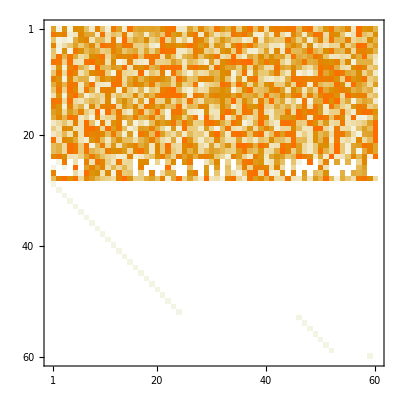

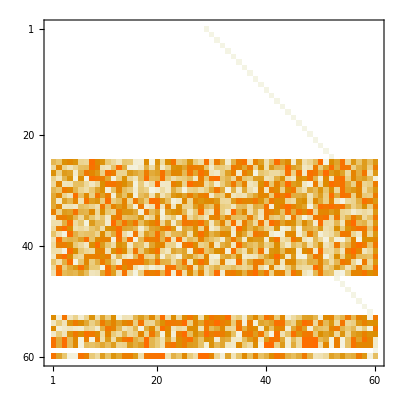

```mathematica
np1//ArrayReshape[#,{60,60}]&//MatrixPlot
np2//ArrayReshape[#,{60,60}]&//MatrixPlot
```

```mathematica
GroebnerBasis[syst // ReplaceAll[{m2->1,s->11,t->17}],variables,MonomialOrder->DegreeReverseLexicographic]; // AbsoluteTiming
```

{8.07019,Null}

```mathematica
gb=GroebnerBasis[syst // ReplaceAll[{m2->1,s->11,t->17}],variables,MonomialOrder->DegreeReverseLexicographic,Modulus->FFPrimeNo[0]]; // AbsoluteTiming
cmatsList=PolynomialReduce[Outer[Times,irreds,variables]//Flatten,gb,variables,MonomialOrder->DegreeReverseLexicographic,Modulus->FFPrimeNo[0]] // Map[Last]; // AbsoluteTiming
```

{5.48073,Null}

{35.1243,Null}

## Hexabox

```mathematica
baikMC = ;
vars={x10,x11,x12,x13}
```

{x10,x11,x12,x13}

```mathematica
ksub = {s12->1,s123->2,s23->3,s234->5,s34->7,s345->11,s45->13,s56->17};
ksub
```

{s12→1,s123→2,s23→3,s234→5,s34→7,s345→11,s45→13,s56→17}

```mathematica
system = {1-x0*baikMC}~Join~D[baikMC,{vars}]// ReplaceAll[ksub];
system // Variables//Sort
```

{s16,x0,x10,x11,x12,x13}

```mathematica
variables = vars~Join~{x0}
```

{x10,x11,x12,x13,x0}

```mathematica
irreds=FindIrreducibleMonomials[system,variables,"MonomialOrder"->DegreeReverseLexicographic]
```

{x10 x11,x11^2,x10 x12,x11 x12,x12^2,x10 x13,x11 x13,x12 x13,x13^2,x0 x10,x0 x11,x0 x12,x0 x13,x0^2,x10,x11,x12,x13,x0,1}

```mathematica
cmats = BuildCompanionMatrices[system,variables,10,irreds,"MonomialOrder"->DegreeReverseLexicographic,"PrintDebugInfo"->2]; // AbsoluteTiming
cmats
```

creating system seeds...done: 0.007104s

generating and sorting monomials...done: 0.773106s

preparing to generate system of size 15115 x 13935...done: 0.235871s

generating system...done: 0.929765s

building FiniteFlow Graph...done: 0.004242s

loading system data into FiniteFlow Graph...done: 0.866699s

learning irreducible monomials...done: 1.01526s

final number of equations needed: 2728

{4.26253,Null}

{ffGraph$500189473541763,{s16,extraparam},{DepVars→{targ[1],targ[2],targ[3],targ[4],targ[5],targ[6],targ[7],targ[8],targ[9],targ[10],targ[11],targ[12],targ[13],targ[14],targ[15],targ[16],targ[17],targ[18],targ[19],targ[20],targ[21],targ[22],targ[23],targ[24],targ[25],targ[26],targ[27],targ[28],targ[29],targ[30],targ[31],targ[32],targ[33],targ[34],targ[35],targ[36],targ[37],targ[38],targ[39],targ[40],targ[41],targ[42],targ[43],targ[44],targ[45],targ[46],targ[47],targ[48],targ[49],targ[50],targ[51],targ[52],targ[53],targ[54],targ[55],targ[56],targ[57],targ[58],targ[59],targ[60],targ[61],targ[62],targ[63],targ[64],targ[65],targ[66],targ[67],targ[68],targ[69],targ[70],targ[71],targ[72],targ[73],targ[74],targ[75],targ[76],targ[77],targ[78],targ[79],targ[80],targ[81],targ[82],targ[83],targ[84],targ[85],targ[86],targ[87],targ[88],targ[89],targ[90],targ[91],targ[92],targ[93],targ[94],targ[95],targ[96],targ[97],targ[98],targ[99],targ[100]},IndepVars→{j[1,1,0,0,0],j[0,2,0,0,0],j[1,0,1,0,0],j[0,1,1,0,0],j[0,0,2,0,0],j[1,0,0,1,0],j[0,1,0,1,0],j[0,0,1,1,0],j[0,0,0,2,0],j[1,0,0,0,1],j[0,1,0,0,1],j[0,0,1,0,1],j[0,0,0,1,1],j[0,0,0,0,2],j[1,0,0,0,0],j[0,1,0,0,0],j[0,0,1,0,0],j[0,0,0,1,0],j[0,0,0,0,1],j[0,0,0,0,0]},SparseOutput→False},{SPQR`Private`m[cmatx10],SPQR`Private`m[cmatx11],SPQR`Private`m[cmatx12],SPQR`Private`m[cmatx13],SPQR`Private`m[cmatx0]},{x10,x11,x12,x13,x0}}

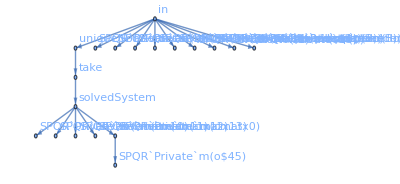

```mathematica
cmats // First // FFGraphDraw
```

```mathematica
FFGraphOutput[cmats//First,"solvedSystem"]
FFGraphEvaluate[cmats // First, {3,5}]; // AbsoluteTiming
```

{0.071497,Null}

```mathematica
?FFGraphOutput
```

```mathematica
(*override to check full graph*)
```

```mathematica
targ = BuildTargetCompanionMatrix[x0,cmats]
```

{ffGraph$500189473541763,{s16,extraparam},SPQR`Private`m[o$45],{j[1,1,0,0,0],j[0,2,0,0,0],j[1,0,1,0,0],j[0,1,1,0,0],j[0,0,2,0,0],j[1,0,0,1,0],j[0,1,0,1,0],j[0,0,1,1,0],j[0,0,0,2,0],j[1,0,0,0,1],j[0,1,0,0,1],j[0,0,1,0,1],j[0,0,0,1,1],j[0,0,0,0,2],j[1,0,0,0,0],j[0,1,0,0,0],j[0,0,1,0,0],j[0,0,0,1,0],j[0,0,0,0,1],j[0,0,0,0,0]},{x10,x11,x12,x13,x0}}

```mathematica
np1=FFGraphEvaluate[targ // First, {3,5}]; // AbsoluteTiming
np1 // Length
np1 // First
```

{0.070163,Null}

2000

6044384382691494011

```mathematica
np1 // ArrayReshape[#,{20,20}]&//Det[#,Modulus->FFPrimeNo[0]]&; // AbsoluteTiming
```

{0.000245,Null}

```mathematica
?FFGraphEvaluateMany
```

```mathematica
?FFReconstructFromCurrentEvaluations
```